## Init

```mathematica
addToPathRecursive[root_]:=Module[{fullRoot,allDirs},fullRoot=ExpandFileName[root];
allDirs=Select[FileNames["*",fullRoot,Infinity],DirectoryQ[#]&&!StringMatchQ[FileNameTake[#],".*"]&];
allDirs=DeleteDuplicates[Prepend[allDirs,fullRoot]];
Do[If[!MemberQ[$Path,dir],AppendTo[$Path,dir]],{dir,allDirs}];];

goUpDirectories[path_String,n_Integer:1]:=Module[{parts},parts=FileNameSplit[ExpandFileName[path]];
FileNameJoin[Take[parts,Length[parts]-n]]];
replaceUniqueSymbols[expr_]:=expr/. s_Symbol:>ToExpression[StringReplace[SymbolName[s],"$"~~NumberString->""]];
addToPathRecursive[goUpDirectories[NotebookDirectory[],2]];
```

```mathematica
Needs["StringCode`"]
```

```mathematica
StringCode`InitStringCode[<|"theory" -> "TypeII","conventions"-> "TypeII-Ashoke"|>]
```

```mathematica
Timing[TaylorAtOrder[R[c[1,z],c[0,z],ct[1,z],ct[0,z]],1,1,0,0]]
```

{0.00331,z^2 R[c[0,0],c[2,0],ct[0,0],ct[2,0]]}

```mathematica
Timing[Bracket[SF[c[0], ct[0],dX[μ,0], dXt[μ,0]], SF[c[0],ct[0],dX[ν,0], dXt[ν,0]]]]
```

{0.029515,0}

```mathematica
Timing[Bracket[SF[c[0], ct[0], expϕf[-1], expϕtf[-1],ψ[μ,0], ψt[μ,0]], SF[c[0], ct[0], expϕf[-1], expϕtf[-1],ψ[ν,0], ψt[ν,0]]]]//Expand
```

{0.152039,0}

```mathematica
datalst = {0.008872,0.059077,0.009966,0.06889,0.019706,0.07535,0.018491,0.120655,0.007606,0.03242,0.011827,0.089383,0.085115,0.1575,0.013528,0.037848,0.011871,0.057874,0.146642,0.016748,0.042054,0.010344,0.095291,0.139766,0.013359,0.052048,0.009911,0.098288,0.059199,0.23436,0.013791,0.047481,0.014748,0.120096,0.118489,0.058958,0.311228,0.006664,0.042192,0.042613,0.092649,0.007457,0.021719,0.00701,0.035076,0.008892,0.04555,0.094573,0.006194,0.021469,0.010953,0.072552,0.008087,0.033405,0.069471,0.005686,0.021825,0.010722,0.073361,0.010565,0.095529,0.10066,0.051968,0.258425,0.005938,0.02533,0.007526,0.023351,0.009311,0.040161,0.0115,0.075328,0.013622,0.072439,0.047653,0.179849,0.007543,0.021618,0.010521,0.072717,0.004499,0.021345,0.02093,0.046748,0.003536,0.01173,0.022664,0.008511,0.016635,0.038148,0.006037,0.016886,0.038021,0.004304,0.013671,0.013843,0.030633,0.011592,0.059513,0.058622,0.115202,0.00591,0.021989,0.049903,0.004512,0.010308,0.023028,0.012354,0.04463,0.085216,0.005729,0.016536,0.0382,0.003891,0.013945,0.03308,0.01045,0.057539,0.121173,0.006307,0.042045,0.040236,0.07952,0.004423,0.023046,0.015019,0.057909,0.00627,0.039938,0.024461,0.096082,0.008995,0.042935,0.024134,0.094791,0.003401,0.013464,0.013508,0.030625,0.009058,0.058372,0.054215,0.118383,0.00781,0.051992,0.048259,0.023537,0.12538,0.003338,0.019067,0.022963,0.004074,0.01232,0.025472,0.006459,0.018124,0.038331,0.009749,0.045281,0.091547,0.007583,0.042777,0.026079,0.101875,0.003369,0.022895,0.043547,0.008049,0.060034,0.123657,0.007066,0.045725,0.072749,0.004537,0.027239,0.01877,0.058274,0.010864,0.090282,0.059116,0.231287,0.005852,0.027836,0.059372,0.004503,0.02873,0.027879,0.013835,0.074509,0.01332,0.114367,0.127085,0.067903,0.321242,0.009371,0.085379,0.076243,0.038168,0.214034,0.00473,0.025146,0.014835,0.057579,0.004975,0.022799,0.01471,0.05691,0.006013,0.03693,0.023505,0.092762,0.011161,0.08818,0.057351,0.220896,0.011152,0.061409,0.039017,0.148449,0.004216,0.033358,0.030152,0.015436,0.083385,0.008926,0.118697,0.118212,0.056784,0.300032};
```

```mathematica
{datalst//Length, datalst//Mean, datalst//Median, datalst//Total, Select[datalst, # < 0.15 &]//Length,  Select[datalst, # < 0.15 &]//Total, datalst//Kurtosis, datalst//MedianDeviation}
```

{229,0.0484448,0.027879,11.0939,219,8.66501,10.2126,0.020069}

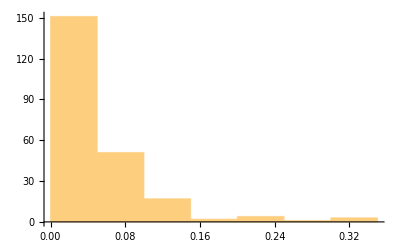

```mathematica
Histogram[datalst, 10]
```

```mathematica
datalst2 =Join @@{{0.011086,0.148203,0.143677,0.083061,0.230669},{0.014111,0.080688,0.083733,0.072906,0.177751},{0.013853,0.081231,0.082332,0.058594,0.161089},{0.011521,0.114018,0.112277,0.064194,0.23686},{0.006521,0.029419,0.029437,0.025211,0.063195},{0.008796,0.051747,0.051384,0.028608,0.112336},{0.009798,0.038863,0.039248,0.025367,0.086096},{0.007861,0.039845,0.037322,0.025292,0.081218},{0.00921,0.033401,0.031778,0.025639,0.06371},{0.00883,0.052559,0.050076,0.02537,0.107665},{0.01218,0.070569,0.07538,0.042675,0.156975},{0.012909,0.085506,0.085378,0.05581,0.22131},{0.01133,0.056332,0.055155,0.043299,0.117745},{0.010144,0.115908,0.114778,0.056091,0.297828},{0.006668,0.042668,0.042366,0.021466,0.094499},{0.005968,0.023994,0.023909,0.023067,0.050438},{0.008723,0.043471,0.041175,0.033977,0.101581},{0.007739,0.044889,0.045954,0.021919,0.090406},{0.005485,0.023876,0.025421,0.020661,0.049978},{0.018547,0.091375,0.090489,0.068231,0.192354},{0.008263,0.032796,0.032233,0.021878,0.068629},{0.005629,0.033208,0.030969,0.020574,0.066461},{0.012522,0.123885,0.121733,0.068377,0.248744},{0.011156,0.091087,0.091036,0.045386,0.235082},{0.006914,0.024327,0.028052,0.020964,0.051077},{0.005536,0.024693,0.026088,0.021081,0.051498},{0.008962,0.045869,0.04111,0.033093,0.086029},{0.012203,0.093532,0.09312,0.068875,0.18747},{0.013017,0.074282,0.068512,0.0452,0.177782},{0.008729,0.032599,0.031461,0.020764,0.067231},{0.014501,0.121953,0.12239,0.070279,0.256778},{0.004299,0.020738,0.02139,0.011079,0.046525},{0.003339,0.013302,0.010803,0.007019,0.022853},{0.006241,0.016888,0.017124,0.011469,0.035019},{0.004426,0.016049,0.0161,0.012191,0.035304},{0.003254,0.013373,0.01311,0.00706,0.029407},{0.008367,0.056247,0.053475,0.026723,0.11287},{0.004396,0.021209,0.022654,0.011079,0.046985},{0.00343,0.010508,0.010047,0.00703,0.024358},{0.007747,0.04303,0.040269,0.027019,0.084077},{0.004398,0.017982,0.01699,0.012077,0.035519},{0.003245,0.015599,0.01355,0.010015,0.029681},{0.008275,0.058269,0.053894,0.027007,0.113462},{0.005986,0.03746,0.035942,0.018598,0.078258},{0.004691,0.023385,0.024731,0.014844,0.060899},{0.006553,0.041869,0.038289,0.024441,0.098263},{0.006997,0.037938,0.037154,0.02444,0.095014},{0.003433,0.013632,0.013719,0.007009,0.02991},{0.008528,0.056709,0.053889,0.027342,0.114351},{0.006141,0.051703,0.048903,0.02346,0.126366},{0.003296,0.010489,0.010532,0.007173,0.025126},{0.0049,0.010498,0.010392,0.00726,0.023149},{0.004887,0.016998,0.016573,0.012319,0.03582},{0.011728,0.043121,0.040231,0.026726,0.084102},{0.005897,0.036773,0.036288,0.023859,0.093599},{0.003223,0.013565,0.013794,0.007272,0.030889},{0.009349,0.058308,0.054416,0.027574,0.11535},{0.008282,0.037475,0.035933,0.018521,0.078396},{0.004906,0.023254,0.02835,0.015241,0.058896},{0.013474,0.091464,0.091962,0.060835,0.229835},{0.008042,0.028315,0.027332,0.018661,0.058432},{0.004667,0.030277,0.030372,0.014918,0.078808},{0.014255,0.122729,0.121584,0.064449,0.307796},{0.008378,0.080126,0.078749,0.03833,0.201826},{0.005929,0.024666,0.026094,0.014846,0.058864},{0.004626,0.023898,0.025763,0.014848,0.059236},{0.005972,0.042223,0.037097,0.024191,0.095629},{0.013923,0.094218,0.089966,0.058689,0.236018},{0.009711,0.062339,0.060508,0.038405,0.150371},{0.005069,0.030828,0.029993,0.014853,0.078231},{0.013993,0.122642,0.119611,0.059624,0.307129}};
```

```mathematica
{datalst2//Length, datalst2//Mean, datalst2//Median, datalst2//Total, Select[datalst2, # < 0.15 &]//Length,  Select[datalst2, # < 0.15 &]//Total, datalst2//Kurtosis, datalst2//MedianDeviation}
```

{355,0.0494167,0.030372,17.5429,336,13.3292,9.10802,0.020705}

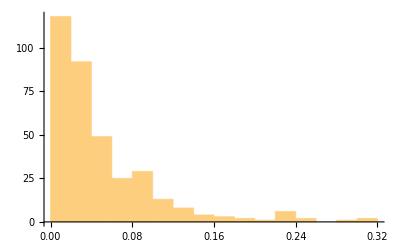

```mathematica
Histogram[datalst2, 10]
```

```mathematica
Timing[actBRST[SF[c[0], expϕb[-2], ξ[1]]]]
```

{0.083249,0}

```mathematica
Timing[1/2(actBRST[SF[c[1],c[0], ct[0], expϕf[-1],ψ[μ,0], expϕtb[-2], ξt[1]]]+ actBRST[SF[ct[1],c[0], ct[0], expϕf[-1],ψ[μ,0], expϕtb[-2], ξt[1]]] + actBRST[SF[c[1],c[0], ct[0], expϕb[-2], ξ[1], expϕtf[-1],ψt[μ,0]]] + actBRST[SF[ct[1],c[0], ct[0], expϕb[-2], ξ[1], expϕtf[-1],ψt[μ,0]]])//Expand//ContractDelta]
```

{1.39349,-1/4 R[c[0,0],ct[0,0],expϕf[-1,0],ηt[0,0],ψ[μ,0,0]]-1/4 R[c[0,0],ct[0,0],expϕtf[-1,0],η[0,0],ψt[μ,0,0]]}

```mathematica
OPE[R[c[w,0]],R[ProfileX[h[m,n],1,{},z,zbar], dX[n,0,z]],R[ProfileX[g[m,n],1,{},w,wbar],dX[m,0,w]],R[c[z,0]]]
```

1/(4 (w-z) (-w+z))((-w+z) (-wbar+zbar))^(1/2 dot[StringCode`OPE`Private`k$8294,StringCode`OPE`Private`k$8295]) ProfileX[g[m,n],1,{n},StringCode`OPE`Private`k$8295] ProfileX[h[m,n],1,{m},StringCode`OPE`Private`k$8294] R[c[w,0],c[z,0],expX[StringCode`OPE`Private`k$8294,z,zbar],expX[StringCode`OPE`Private`k$8295,w,wbar]]-1/(2 (-w+z))((-w+z) (-wbar+zbar))^(1/2 dot[StringCode`OPE`Private`k$8294,StringCode`OPE`Private`k$8295]) ProfileX[g[m,n],1,{n},StringCode`OPE`Private`k$8295] ProfileX[h[m,n],1,{},StringCode`OPE`Private`k$8294] R[c[w,0],c[z,0],dX[m,0,w],expX[StringCode`OPE`Private`k$8294,z,zbar],expX[StringCode`OPE`Private`k$8295,w,wbar]]-1/(2 (w-z))((-w+z) (-wbar+zbar))^(1/2 dot[StringCode`OPE`Private`k$8294,StringCode`OPE`Private`k$8295]) ProfileX[g[m,n],1,{},StringCode`OPE`Private`k$8295] ProfileX[h[m,n],1,{m},StringCode`OPE`Private`k$8294] R[c[w,0],c[z,0],dX[n,0,z],expX[StringCode`OPE`Private`k$8294,z,zbar],expX[StringCode`OPE`Private`k$8295,w,wbar]]+((-w+z) (-wbar+zbar))^(1/2 dot[StringCode`OPE`Private`k$8294,StringCode`OPE`Private`k$8295]) ProfileX[g[m,n],1,{},StringCode`OPE`Private`k$8295] ProfileX[h[m,n],1,{},StringCode`OPE`Private`k$8294] R[c[w,0],c[z,0],dX[m,0,w],dX[n,0,z],expX[StringCode`OPE`Private`k$8294,z,zbar],expX[StringCode`OPE`Private`k$8295,w,wbar]]-1/(2 (-w+z)^2)((-w+z) (-wbar+zbar))^(1/2 dot[StringCode`OPE`Private`k$8294,StringCode`OPE`Private`k$8295]) ProfileX[g[m,n],1,{},StringCode`OPE`Private`k$8295] ProfileX[h[m,n],1,{},StringCode`OPE`Private`k$8294] R[c[w,0],c[z,0],expX[StringCode`OPE`Private`k$8294,z,zbar],expX[StringCode`OPE`Private`k$8295,w,wbar]] δ[n,m]

```mathematica
List @@ (-1/z+R[dϕ[0,0]]-z R[η[0,0],ξ[1,0]]-z^2 R[η[0,0],ξ[2,0]]+z^2 R[dϕ[0,0],η[0,0],ξ[1,0]]+z^3 R[dϕ[0,0],η[0,0],ξ[2,0]])
```

{-1/z,R[dϕ[0,0]],-z R[η[0,0],ξ[1,0]],-z^2 R[η[0,0],ξ[2,0]],z^2 R[dϕ[0,0],η[0,0],ξ[1,0]],z^3 R[dϕ[0,0],η[0,0],ξ[2,0]]}

```mathematica
ExtractZPowers[exprs_List]:=Cases[exprs,Power[z,n_]:>n,(*Matches z^n*){0,Infinity}              (*Search at all levels*)]~Join~Cases[exprs,z:>1,(*Matches linear z*){0,Infinity}]~Join~Cases[exprs,Rational[-1,z]:>-1,(*Matches-1/z*){0,Infinity}]
```

```mathematica
ExtractZPowers[List @@ (-1/z+R[dϕ[0,0]]-z R[η[0,0],ξ[1,0]]-z^2 R[η[0,0],ξ[2,0]]+z^2 R[dϕ[0,0],η[0,0],ξ[1,0]]+z^3 R[dϕ[0,0],η[0,0],ξ[2,0]])]
```

{-1,2,2,3,1,1,1,1,1}

```mathematica
Series[((-w+z) (-wbar+zbar))^(1/2 StringCode`OPE`Private`k$5211[m] StringCode`OPE`Private`k$5212[m]),{StringCode`OPE`Private`k$5211[m] ,0,2}]
```

1+1/2 StringCode`OPE`Private`k$5212[m] Log[(-w+z) (-wbar+zbar)] StringCode`OPE`Private`k$5211[m]+1/8 (StringCode`OPE`Private`k$5212[m])^2 Log[(-w+z) (-wbar+zbar)]^2 (StringCode`OPE`Private`k$5211[m])^2+O[StringCode`OPE`Private`k$5211[m]]^3

```mathematica
colors={Red,Green,Blue};
pairs=Subsets[colors,{2}];

capacities=<|Red->1,Green->2,Blue->3|>;

(*For each pair,allow:not used (None),or assigned to one of its two colors*)
pairChoices={None,#[[1]],#[[2]]}&/@pairs;

(*All combinations:3 options (None or 2 slots) per pair*)
allAssignments=Tuples[pairChoices];

(*Filter valid assignments:no slot exceeds its capacity*)
validAssignments=Select[allAssignments,Function[assignment,Module[{usedSlots,counts},usedSlots=DeleteCases[assignment,None];
counts=Counts[usedSlots];
AllTrue[colors,Function[c,Lookup[counts,c,0]<=capacities[c]]]]]];

validAssignments
```

{{None,None,None},{None,None,RGBColor[0, 1, 0]},{None,None,RGBColor[0, 0, 1]},{None,RGBColor[1, 0, 0],None},{None,RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{None,RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{None,RGBColor[0, 0, 1],None},{None,RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{None,RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],None,None},{RGBColor[1, 0, 0],None,RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],None,RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],None},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],None,None},{RGBColor[0, 1, 0],None,RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],None,RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],None},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],None},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}}

# Testing

```mathematica
Gmatter[z]
```

ⅈ √2 R[dX[μ$5129,0,z],ψ[μ$5129,0,z]]

```mathematica
(*** testing β γ OPE ***)
Taylor[(OPE[βghost[z],γghost[w]]//Expand)/.w->0,0,0,1]//Expand
Taylor[(OPE[γghost[z],βghost[w]]//Expand)/.w->0,0,0,1]//Expand
```

-1/z+R[dϕ[0,0]]-z R[η[0,0],ξ[1,0]]-z^2 R[η[0,0],ξ[2,0]]+z^2 R[dϕ[0,0],η[0,0],ξ[1,0]]+z^3 R[dϕ[0,0],η[0,0],ξ[2,0]]

1/z+R[dϕ[0,0]]+z R[η[0,0],ξ[1,0]]+z^2 R[η[1,0],ξ[1,0]]+z^2 R[dϕ[0,0],η[0,0],ξ[1,0]]+z^3 R[dϕ[0,0],η[1,0],ξ[1,0]]

```mathematica
(*** checking BRST transformation of b and β ghosts ***)
Polar[Taylor[OPE[jBRST[z],R[b[0,w]]]/.w->0//Expand,0,0,2],z,0]-1/z Ttotal[0]//Expand//replaceUniqueSymbols
Polar[Taylor[OPE[jBRST[z],R[βghost[w]]]/.w->0//Expand,0,0,2],z,0]- 1/z (-1/2  Gtotal[0])//Expand//replaceUniqueSymbols
```

-(3 R[dϕ[0,0]])/(2 z^2)-R[b[0,0],c[0,0]]/z^2

0

```mathematica
(*** checking PCO ***)
Polar[Taylor[(OPE[jBRST[z],R[ξ[0,w]]]//Expand)/.w->0,0,0,2],z,0]-1/z PCO[0]//Expand//replaceUniqueSymbols
```

R[b[0,0],expϕb[2,0],η[0,0]]/(4 z^2)

```mathematica
(*** checking BRST current is weight 1 primary ***)
pol1=Polar[Taylor[(OPE[Ttotal[z],jBRST[w]]//Expand//Contract)/.w->0,0,0,2],z,0];
pol2=Polar[Taylor[jBRST[z]/z^2,0,0,2],z,0];
(pol1- pol2//replaceUniqueSymbols)/.{δ[μ,μ]->1}//Expand
```

0

```mathematica
(*** checking nilpotency of BRST charge ***)
poltest=Polar[Taylor[(OPE[jBRST[z],jBRST[w]]//Expand//Contract)/.w->0,0,0,3],z,0]
```

-(5 R[c[0,0],c[1,0]])/(2 z^3)+1/(4 z^2)(-5 R[c[0,0],c[2,0]]-2 ⅈ √2 R[c[0,0],dX[μ$5224,0,0],expϕf[1,0],η[0,0],ψ[μ$5224,0,0]]+2 ⅈ √2 R[c[0,0],dX[μ$5226,0,0],expϕf[1,0],η[0,0],ψ[μ$5226,0,0]]-2 R[c[0,0],c[1,0],ψ[μ$5223,0,0],ψ[μ$5225,0,0]] δ[μ$5223,μ$5225]+2 ⅈ √2 R[c[0,0],dX[μ$5223,0,0],expϕf[1,0],η[0,0],ψ[μ$5226,0,0]] δ[μ$5223,μ$5226]+ⅈ √2 R[c[0,0],dX[μ$5226,0,0],expϕf[1,0],η[0,0],ψ[μ$5223,0,0]] δ[μ$5223,μ$5226]-ⅈ √2 R[c[0,0],dX[μ$5224,0,0],expϕf[1,0],η[0,0],ψ[μ$5225,0,0]] δ[μ$5224,μ$5225]-2 ⅈ √2 R[c[0,0],dX[μ$5225,0,0],expϕf[1,0],η[0,0],ψ[μ$5224,0,0]] δ[μ$5224,μ$5225]+R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5224,0,0],ψ[μ$5226,0,0]] δ[μ$5224,μ$5226])+1/(8 z)(-R[expϕb[2,0],η[0,0],η[3,0]]-R[expϕb[2,0],η[1,0],η[2,0]]-8 R[c[0,0],c[1,0],dX[μ$5223,0,0],dX[μ$5223,0,0]]-8 R[c[0,0],c[1,0],dX[μ$5225,0,0],dX[μ$5225,0,0]]-4 R[c[0,0],c[1,0],ψ[μ$5223,0,0],ψ[μ$5223,1,0]]-4 R[c[0,0],c[1,0],ψ[μ$5225,0,0],ψ[μ$5225,1,0]]-5 R[dϕ[0,0],expϕb[2,0],η[0,0],η[2,0]]-3 R[dϕ[1,0],expϕb[2,0],η[0,0],η[1,0]]-2 R[b[0,0],c[0,0],expϕb[2,0],η[0,0],η[2,0]]-2 R[b[0,0],c[1,0],expϕb[2,0],η[0,0],η[1,0]]-2 R[b[1,0],c[0,0],expϕb[2,0],η[0,0],η[1,0]]-4 ⅈ √2 R[c[0,0],dX[μ$5224,0,0],expϕf[1,0],η[0,0],ψ[μ$5224,1,0]]-4 ⅈ √2 R[c[0,0],dX[μ$5224,1,0],expϕf[1,0],η[0,0],ψ[μ$5224,0,0]]+4 ⅈ √2 R[c[0,0],dX[μ$5226,0,0],expϕf[1,0],η[1,0],ψ[μ$5226,0,0]]-6 ⅈ √2 R[c[1,0],dX[μ$5224,0,0],expϕf[1,0],η[0,0],ψ[μ$5224,0,0]]-2 ⅈ √2 R[c[1,0],dX[μ$5226,0,0],expϕf[1,0],η[0,0],ψ[μ$5226,0,0]]+2 R[dX[μ$5223,0,0],dX[μ$5223,0,0],expϕb[2,0],η[0,0],η[1,0]]+2 R[dX[μ$5225,0,0],dX[μ$5225,0,0],expϕb[2,0],η[0,0],η[1,0]]-6 R[dϕ[0,0],dϕ[0,0],expϕb[2,0],η[0,0],η[1,0]]+R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5223,0,0],ψ[μ$5223,1,0]]+R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5225,0,0],ψ[μ$5225,1,0]]-4 R[b[0,0],c[0,0],dϕ[0,0],expϕb[2,0],η[0,0],η[1,0]]+4 ⅈ √2 R[c[0,0],dX[μ$5226,0,0],dϕ[0,0],expϕf[1,0],η[0,0],ψ[μ$5226,0,0]]+16 R[c[0,0],c[1,0],dX[μ$5223,0,0],dX[μ$5225,0,0]] δ[μ$5223,μ$5225]+2 R[c[0,0],c[1,0],ψ[μ$5223,0,0],ψ[μ$5225,1,0]] δ[μ$5223,μ$5225]-6 R[c[0,0],c[1,0],ψ[μ$5223,1,0],ψ[μ$5225,0,0]] δ[μ$5223,μ$5225]-2 R[c[0,0],c[2,0],ψ[μ$5223,0,0],ψ[μ$5225,0,0]] δ[μ$5223,μ$5225]+4 ⅈ √2 R[c[0,0],dX[μ$5223,1,0],expϕf[1,0],η[0,0],ψ[μ$5226,0,0]] δ[μ$5223,μ$5226]+4 ⅈ √2 R[c[0,0],dX[μ$5226,0,0],expϕf[1,0],η[0,0],ψ[μ$5223,1,0]] δ[μ$5223,μ$5226]+4 ⅈ √2 R[c[1,0],dX[μ$5223,0,0],expϕf[1,0],η[0,0],ψ[μ$5226,0,0]] δ[μ$5223,μ$5226]+2 ⅈ √2 R[c[1,0],dX[μ$5226,0,0],expϕf[1,0],η[0,0],ψ[μ$5223,0,0]] δ[μ$5223,μ$5226]+2 ⅈ √2 R[c[0,0],dX[μ$5224,0,0],expϕf[1,0],η[0,0],ψ[μ$5225,1,0]] δ[μ$5224,μ$5225]-2 ⅈ √2 R[c[0,0],dX[μ$5224,0,0],expϕf[1,0],η[1,0],ψ[μ$5225,0,0]] δ[μ$5224,μ$5225]-2 ⅈ √2 R[c[0,0],dX[μ$5224,1,0],expϕf[1,0],η[0,0],ψ[μ$5225,0,0]] δ[μ$5224,μ$5225]-4 ⅈ √2 R[c[0,0],dX[μ$5225,0,0],expϕf[1,0],η[0,0],ψ[μ$5224,1,0]] δ[μ$5224,μ$5225]-4 ⅈ √2 R[c[0,0],dX[μ$5225,0,0],expϕf[1,0],η[1,0],ψ[μ$5224,0,0]] δ[μ$5224,μ$5225]-2 ⅈ √2 R[c[0,0],dX[μ$5224,0,0],dϕ[0,0],expϕf[1,0],η[0,0],ψ[μ$5225,0,0]] δ[μ$5224,μ$5225]-4 ⅈ √2 R[c[0,0],dX[μ$5225,0,0],dϕ[0,0],expϕf[1,0],η[0,0],ψ[μ$5224,0,0]] δ[μ$5224,μ$5225]-4 R[dX[μ$5224,0,0],dX[μ$5226,0,0],expϕb[2,0],η[0,0],η[1,0]] δ[μ$5224,μ$5226]+2 R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5224,1,0],ψ[μ$5226,0,0]] δ[μ$5224,μ$5226]+R[expϕb[2,0],η[0,0],η[2,0],ψ[μ$5224,0,0],ψ[μ$5226,0,0]] δ[μ$5224,μ$5226]+2 R[dϕ[0,0],expϕb[2,0],η[0,0],η[1,0],ψ[μ$5224,0,0],ψ[μ$5226,0,0]] δ[μ$5224,μ$5226])

```mathematica
poltotalderiv=Polar[Taylor[-1/(8 z^2)2 ⅈ √2 R[c[0,z],dX[μ,0,z],expϕf[1,z],η[0,z],ψ[μ,0,z]]-R[b[0,z],c[0,z],expϕb[2,z],η[0,z],η[1,z]]/(4 z^2)+(-R[expϕb[2,z],η[0,z],η[2,z]])/(8 z^2)+(-3 R[dϕ[0,z],expϕb[2,z],η[0,z],η[1,z]])/(8 z^2),0,0,2],z,0];
((poltest-  poltotalderiv//replaceUniqueSymbols)/.{δ[μ,μ]->1})+O[z]
```

-(5 R[c[0,0],c[1,0]])/(2 z^3)+1/(8 z^2)(-10 R[c[0,0],c[2,0]]+R[expϕb[2,0],η[0,0],η[2,0]]+3 R[dϕ[0,0],expϕb[2,0],η[0,0],η[1,0]]+2 R[b[0,0],c[0,0],expϕb[2,0],η[0,0],η[1,0]]+2 ⅈ √2 R[c[0,0],dX[μ,0,0],expϕf[1,0],η[0,0],ψ[μ,0,0]])+O[z]^1

```mathematica
(*** checking T T OPE ***)
(Polar[Taylor[((OPE[Ttotal[z],Ttotal[w]]//Simplify//Contract)/.w->0)-(1/z^2 Ttotal[0]+1/z^2 Ttotal[z]),0,0,2],z,0]//replaceUniqueSymbols)/.{δ[μ,μ]->1}//Expand
```

0

```mathematica
tripgrav=OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar],RaisedGraviton[μ3,ν3,k3,z3,z3bar]];
```

```mathematica
Graviton[μ_,ν_,k_,z_,zbar_]:=R[c[0,z],ct[0,zbar],expϕf[-1,z],ψ[μ,0,z],expϕtf[-1,zbar],ψt[ν,0,zbar],expX[k,z,zbar]]

PictureRaiseL[vert_,z1_,z1bar_]:=Block[{w,x},SeriesCoefficient[(Taylor[OPE[PCO[w],vert]//ContractDelta,z1,z1bar,0]/.w->z1+x)+O[x],0]]
PictureRaiseR[vert_,z1_,z1bar_]:=Block[{w,x},SeriesCoefficient[(Taylor[OPE[PCObar[w],vert]//ContractDelta,z1,z1bar,0]/.w->z1bar+x)+O[x],0]]
PictureRaiseLR[vert_,z1_,z1bar_]:=PictureRaiseR[PictureRaiseL[vert,z1,z1bar],z1,z1bar]
```

```mathematica
RaisedGraviton[μ1_,ν1_,k1_,z1_,z1bar_]:=PictureRaiseLR[Graviton[μ1,ν1,k1,z1,z1bar],z1,z1bar]//Expand

tripgrav=OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar],RaisedGraviton[μ3,ν3,k3,z3,z3bar]];

(*** graviton 3-point amplitude ***)tripgravamp=Vev[tripgrav/.{z1->x,z1bar->x,z2->1,z2bar->1,z3->0,z3bar->0}/.{dot[k1,k2]->0,dot[k1,k3]->0,dot[k2,k3]->0}]//Simplify//Expand//ContractDelta//Simplify

(e1[μ1] e1[ν1] e2[μ2] e2[ν2] e3[μ3] e3[ν3] tripgravamp//Expand//ContractDelta)//.{(f1_[μ_] f2_[μ_]):>dot[f1,f2]}/.{dot[e3,k2]->-dot[e3,k1]}//Simplify
```

-1/(32 (-1+x)^2)R[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expϕb[-2,0],expϕtb[-2,0]] (k1[μ3] δ[μ1,μ2]+x k2[μ3] δ[μ1,μ2]-(-1+x) (k3[μ2] δ[μ1,μ3]-k3[μ1] δ[μ2,μ3])) (k1[ν3] δ[ν1,ν2]+x k2[ν3] δ[ν1,ν2]-(-1+x) (k3[ν2] δ[ν1,ν3]-k3[ν1] δ[ν2,ν3]))

-1/32 (-dot[e1,k3] dot[e2,e3]+dot[e1,e3] dot[e2,k3]+dot[e1,e2] dot[e3,k1])^2 R[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expϕb[-2,0],expϕtb[-2,0]]

```mathematica
SimpleRaisedGraviton[μ_,ν_,k_,z_,zbar_]:=(RaisedGraviton[μ,ν,k,z,zbar]/.{η[a__]:>0,ηt[a__]:>0})
IntegratedSimpleRaisedGraviton[μ_,ν_,k_,z_,zbar_]:=Block[{w},(w-z) (w-zbar) OPE[R[bt[0,w],b[0,w]],SimpleRaisedGraviton[μ,ν,k,z,zbar]]/.{b[a__]:>0,bt[a__]:>0}//Simplify//Expand]
FourGravCorr=Corr[OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar]],
OPE[SimpleRaisedGraviton[μ3,ν3,k3,z3,z3bar],IntegratedSimpleRaisedGraviton[μ4,ν4,k4,z4,z4bar]]];
```

```mathematica
FourGravCorr
```

```mathematica
VevFourGravCorr=Vev[FourGravCorr/.{z3->1/x,z3bar->1/x,z1->1,z1bar->1,z2->0,z2bar->0}/.{dot[k1,k4]->dot[k2,k3],dot[k2,k4]->dot[k1,k3],dot[k3,k4]->dot[k1,k2]}]//Simplify
```

1/(256 (-1+x z4)^3 (-1+x z4bar)^3)(1/x^2)^(1/2 dot[k2,k3]) ((-1+x)^2/x^2)^(1/2 dot[k1,k3]) ((-1+z4) (-1+z4bar))^(1/2 (-2+dot[k2,k3])) (z4 z4bar)^(1/2 (-2+dot[k1,k3])) (((-1+x z4) (-1+x z4bar))/x^2)^(1/2 (2+dot[k1,k2])) CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]] (-k2[μ3] k2[μ4] δ[μ1,μ2]+x k2[μ3] k2[μ4] δ[μ1,μ2]+z4 k2[μ3] k2[μ4] δ[μ1,μ2]+x z4 k2[μ3] k2[μ4] δ[μ1,μ2]-2 x^2 z4 k2[μ3] k2[μ4] δ[μ1,μ2]-2 x z4^2 k2[μ3] k2[μ4] δ[μ1,μ2]+x^2 z4^2 k2[μ3] k2[μ4] δ[μ1,μ2]+x^3 z4^2 k2[μ3] k2[μ4] δ[μ1,μ2]+x^2 z4^3 k2[μ3] k2[μ4] δ[μ1,μ2]-x^3 z4^3 k2[μ3] k2[μ4] δ[μ1,μ2]+x z4 k2[μ3] k3[μ4] δ[μ1,μ2]-x^2 z4 k2[μ3] k3[μ4] δ[μ1,μ2]-x z4^2 k2[μ3] k3[μ4] δ[μ1,μ2]+x^3 z4^2 k2[μ3] k3[μ4] δ[μ1,μ2]+x^2 z4^3 k2[μ3] k3[μ4] δ[μ1,μ2]-x^3 z4^3 k2[μ3] k3[μ4] δ[μ1,μ2]-k2[μ4] k4[μ3] δ[μ1,μ2]+x k2[μ4] k4[μ3] δ[μ1,μ2]+z4 k2[μ4] k4[μ3] δ[μ1,μ2]-x^2 z4 k2[μ4] k4[μ3] δ[μ1,μ2]-x z4^2 k2[μ4] k4[μ3] δ[μ1,μ2]+x^2 z4^2 k2[μ4] k4[μ3] δ[μ1,μ2]+x z4 k3[μ4] k4[μ3] δ[μ1,μ2]-x^2 z4 k3[μ4] k4[μ3] δ[μ1,μ2]-x z4^2 k3[μ4] k4[μ3] δ[μ1,μ2]+x^2 z4^2 k3[μ4] k4[μ3] δ[μ1,μ2]+x k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x z4 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-2 x^2 z4 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+2 x^2 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+x^3 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x^3 z4^3 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x^2 z4 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+x^2 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+x^3 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x^3 z4^3 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+2 x z4 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-2 x^2 z4 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x^2 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x^3 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x z4 k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x^2 z4 k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x z4 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+2 x^2 z4 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-2 x^2 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-x^3 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x^3 z4^3 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x^2 z4 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-x^2 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-x^3 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x^3 z4^3 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-z4 (-1+x z4) k1[μ4] ((-1+x) (-1+x z4) k2[μ3] δ[μ1,μ2]-(-1+x) k4[μ3] δ[μ1,μ2]+x (-1+x z4) k3[μ$5628] (δ[μ1,μ$5628] δ[μ2,μ3]-δ[μ1,μ3] δ[μ2,μ$5628]))+k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-2 x z4 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+2 x^2 z4 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+x^2 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x^3 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x z4 k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+x^2 z4 k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+(-1+x z4) k1[μ3] (z4 (-1+x z4) k1[μ4] δ[μ1,μ2]+(-1+z4) (-1+x z4) k2[μ4] δ[μ1,μ2]-x z4 k3[μ4] δ[μ1,μ2]+x z4^2 k3[μ4] δ[μ1,μ2]+k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x z4 k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+x z4 k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630])-2 x z4 δ[μ1,μ2] δ[μ3,μ4]+2 x^2 z4 δ[μ1,μ2] δ[μ3,μ4]+2 x z4^2 δ[μ1,μ2] δ[μ3,μ4]-2 x^2 z4^2 δ[μ1,μ2] δ[μ3,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]-x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]-x k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]+x k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]+x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]+x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]+x k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]+x z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]-x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]-x k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]-x z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]) (k2[ν3] k2[ν4] δ[ν1,ν2]-x k2[ν3] k2[ν4] δ[ν1,ν2]-z4bar k2[ν3] k2[ν4] δ[ν1,ν2]-x z4bar k2[ν3] k2[ν4] δ[ν1,ν2]+2 x^2 z4bar k2[ν3] k2[ν4] δ[ν1,ν2]+2 x z4bar^2 k2[ν3] k2[ν4] δ[ν1,ν2]-x^2 z4bar^2 k2[ν3] k2[ν4] δ[ν1,ν2]-x^3 z4bar^2 k2[ν3] k2[ν4] δ[ν1,ν2]-x^2 z4bar^3 k2[ν3] k2[ν4] δ[ν1,ν2]+x^3 z4bar^3 k2[ν3] k2[ν4] δ[ν1,ν2]-x z4bar k2[ν3] k3[ν4] δ[ν1,ν2]+x^2 z4bar k2[ν3] k3[ν4] δ[ν1,ν2]+x z4bar^2 k2[ν3] k3[ν4] δ[ν1,ν2]-x^3 z4bar^2 k2[ν3] k3[ν4] δ[ν1,ν2]-x^2 z4bar^3 k2[ν3] k3[ν4] δ[ν1,ν2]+x^3 z4bar^3 k2[ν3] k3[ν4] δ[ν1,ν2]+k2[ν4] k4[ν3] δ[ν1,ν2]-x k2[ν4] k4[ν3] δ[ν1,ν2]-z4bar k2[ν4] k4[ν3] δ[ν1,ν2]+x^2 z4bar k2[ν4] k4[ν3] δ[ν1,ν2]+x z4bar^2 k2[ν4] k4[ν3] δ[ν1,ν2]-x^2 z4bar^2 k2[ν4] k4[ν3] δ[ν1,ν2]-x z4bar k3[ν4] k4[ν3] δ[ν1,ν2]+x^2 z4bar k3[ν4] k4[ν3] δ[ν1,ν2]+x z4bar^2 k3[ν4] k4[ν3] δ[ν1,ν2]-x^2 z4bar^2 k3[ν4] k4[ν3] δ[ν1,ν2]+x k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-x z4bar k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-2 x^2 z4bar k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]+2 x^2 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]+x^3 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-x^3 z4bar^3 k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-x^2 z4bar k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]+x^2 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]+x^3 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]-x^3 z4bar^3 k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]-x k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]+x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]-k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+x k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+2 x z4bar k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]-2 x^2 z4bar k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]-x^2 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+x^3 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]-k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]+x k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]+x z4bar k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]-x^2 z4bar k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]-x k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+x z4bar k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+2 x^2 z4bar k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]-2 x^2 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]-x^3 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+x^3 z4bar^3 k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+x^2 z4bar k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]-x^2 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]-x^3 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]+x^3 z4bar^3 k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]-x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]-x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]+x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]+x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]+z4bar (-1+x z4bar) k1[ν4] ((-1+x) (-1+x z4bar) k2[ν3] δ[ν1,ν2]-(-1+x) k4[ν3] δ[ν1,ν2]-x (-1+x z4bar) k3[μ$5629] (δ[ν1,ν3] δ[ν2,μ$5629]-δ[ν1,μ$5629] δ[ν2,ν3]))+k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-x k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-2 x z4bar k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]+2 x^2 z4bar k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]+x^2 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-x^3 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]+k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]-x k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]-x z4bar k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]+x^2 z4bar k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]+x k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]-x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]-(-1+x z4bar) k1[ν3] (z4bar (-1+x z4bar) k1[ν4] δ[ν1,ν2]+(-1+z4bar) (-1+x z4bar) k2[ν4] δ[ν1,ν2]-x z4bar k3[ν4] δ[ν1,ν2]+x z4bar^2 k3[ν4] δ[ν1,ν2]-k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+x z4bar k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-x z4bar k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4])+x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]-x z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]-x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]-x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]-x k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]+x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]+2 x z4bar δ[ν1,ν2] δ[ν3,ν4]-2 x^2 z4bar δ[ν1,ν2] δ[ν3,ν4]-2 x z4bar^2 δ[ν1,ν2] δ[ν3,ν4]+2 x^2 z4bar^2 δ[ν1,ν2] δ[ν3,ν4]-x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]+x z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]+x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]+x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]+x k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4]-x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4])

```mathematica
Prefactor=(-1/x)^dot[k2,k3] ((-1+x)/x)^dot[k1,k3] (1-z4)^(-1+1/2 dot[k2,k3]) (1/x-z4)^(1/2 dot[k1,k2]) (-z4)^(-1+1/2 dot[k1,k3]) (1-z4bar)^(-1+1/2 dot[k2,k3]) (1/x-z4bar)^(1/2 dot[k1,k2]) (-z4bar)^(-1+1/2 dot[k1,k3])/(256 x^2 (-1+x z4)^2 (-1+x z4bar)^2) CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]];
```

```mathematica
TwoFactors=List @@(VevFourGravCorr/Prefactor);
```

```mathematica
PrefactorSimplified=Assuming[x>0,((1/x)^dot[k2,k3] (1/x)^dot[k1,k3] (1-z4)^(-1+1/2 dot[k2,k3]) (1/x)^(1/2 dot[k1,k2]) (z4)^(-1+1/2 dot[k1,k3]) (1-z4bar)^(-1+1/2 dot[k2,k3]) (1/x)^(1/2 dot[k1,k2]) (z4bar)^(-1+1/2 dot[k1,k3]) CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]])/(256 x^2 ) /.{dot[k2,k3]->-dot[k1,k2]-dot[k1,k3]}//Simplify];
```

```mathematica
TwoFactorsSimplified=(((TwoFactors//Expand//ContractDelta)//.{k1[m_] k2[m_]:>dot[k1,k2],k1[m_] k3[m_]:>dot[k1,k3],k1[m_] k4[m_]:>dot[k1,k4],k2[m_] k3[m_]:>dot[k2,k3],k2[m_] k4[m_]:>dot[k2,k4],k3[m_] k4[m_]:>dot[k3,k4]}/.{dot[k1,k4]->dot[k2,k3],dot[k2,k4]->dot[k1,k3],dot[k3,k4]->dot[k1,k2]}/.{dot[k2,k3]->-dot[k1,k2]-dot[k1,k3]})+O[x]^2)/.{k4[m_]:>-k1[m]-k2[m]-k3[m]}/.{k1[μ1]->0,k2[μ2]->0,k3[μ3]->0,k1[ν1]->0,k2[ν2]->0,k3[ν3]->0}//Normal//Simplify;
```

```mathematica
(-x^2) PrefactorSimplified/.{CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]]->-4}
```

1/64 (1-z4)^(1/2 (-2-dot[k1,k2]-dot[k1,k3])) z4^(-1+1/2 dot[k1,k3]) (1-z4bar)^(1/2 (-2-dot[k1,k2]-dot[k1,k3])) z4bar^(-1+1/2 dot[k1,k3])

```mathematica
(-x^2) PrefactorSimplified/.{CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]]->-4}/.{dot[k1,k2]->-1/2 s,dot[k2,k3]->-1/2 t,dot[k1,k3]->-1/2 u}/.{z4^a_ z4bar^a_ (1-z4)^b_ (1-z4bar)^b_:>2Pi Gamma[a+1] Gamma[b+1] Gamma[-1-a-b]/(Gamma[a+b+2] Gamma[-b] Gamma[-a])}//Simplify
```

(π Gamma[1-s/4] Gamma[-u/4] Gamma[(s+u)/4])/(32 Gamma[s/4] Gamma[1-s/4-u/4] Gamma[1+u/4])

```mathematica
TwoFactorsContracted=({e1[μ1]  e2[μ2] e3[μ3] e4[μ4]TwoFactorsSimplified[[1]]/(-x),  e1[ν1]e2[ν2]e3[ν3] e4[ν4]TwoFactorsSimplified[[2]]/x}//Expand//ContractDelta)//.{(f1_[μ_] f2_[μ_]):>dot[f1,f2]}/.{dot[e4,k3]->-dot[e4,k1]-dot[e4,k2]}//Expand;
```

```mathematica
TwoFactorsContracted[[1]]-f1-f2-f3//Expand
```

-f1-f2-f3-((1/x^2)^(1/2 (-dot[k1,k2]-dot[k1,k3])) e1[μ1] e2[μ2] e3[μ3] e4[μ4])/x

```mathematica
f1=Coefficient[TwoFactorsContracted[[1]],dot[e1,e2] dot[e3,e4]] dot[e1,e2] dot[e3,e4]
f2=Coefficient[TwoFactorsContracted[[1]],dot[e1,e3] dot[e2,e4]]dot[e1,e3] dot[e2,e4]
f3=Coefficient[TwoFactorsContracted[[1]],dot[e1,e4] dot[e2,e3]]dot[e1,e4] dot[e2,e3]
```

0

0

0

```mathematica
TripGravGenPCO=Corr[OPE[PCObar[wbar],PCO[w]],OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar],Graviton[μ3,ν3,k3,z3,z3bar]]];
```

$Aborted

```mathematica
(*** graviton 3-point amplitude with PCOs at generic positions ***)
TripGravAmpPCOCorr=Vev[TripGravGenPCO/.{z1->x,z1bar->x,z2->1,z2bar->1,z3->0,z3bar->0}/.{dot[k1,k2]->0,dot[k1,k3]->0,dot[k2,k3]->0}]//Simplify//Expand//ContractDelta//Simplify

((e1[μ1] e1[ν1] e2[μ2] e2[ν2] e3[μ3] e3[ν3] TripGravAmpPCOCorr//Expand//ContractDelta)//.{(f1_[μ_] f2_[μ_]):>dot[f1,f2]}/.{dot[e3,k2]->-dot[e3,k1],dot[e1,k2]->-dot[e1,k3],dot[e2,k1]->-dot[e2,k3],dot[e3,k3]->0,dot[e1,k1]->0,dot[e2,k2]->0})//Simplify
```